```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
```

/home/zack/cantera/ratematrix

data/h2o2/6/

{36,2456,8.02179,496463,19}

-Graphics-

{0.194868,Null}

{0.240371,Null}

{0.233183,Null}

{0.192317,Null}

{0.00205,Null}

{0.001957,Null}

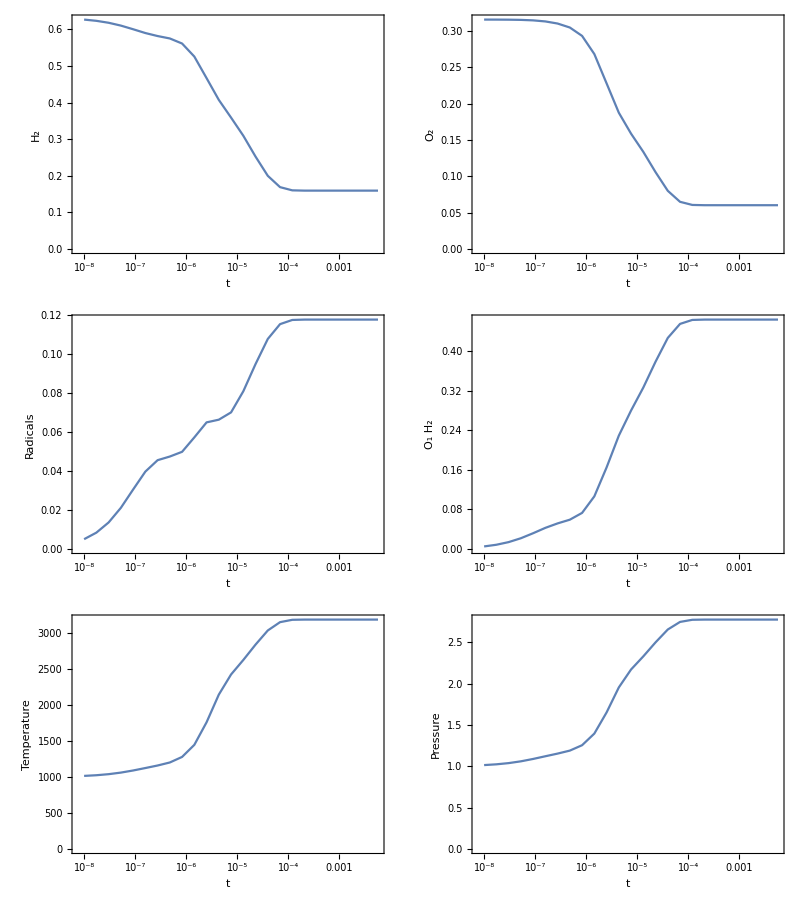

```mathematica
filebase="data/h2o2/6/"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]]
states=Partition[BinaryReadList[filebase<>"propogate.npy","Real64"][[17;;-1]],dim];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
o2norm=DiagonalMatrix[((#[[4]])/Total[#])&/@multiindices];
h2norm=DiagonalMatrix[((#[[1]])/Total[#])&/@multiindices];
h2onorm=DiagonalMatrix[((#[[6]])/Total[#])&/@multiindices];
radicalnorm=DiagonalMatrix[((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices];
radicalnorm=DiagonalMatrix[((#[[2]])/Total[#])&/@multiindices];
temperaturenorm=DiagonalMatrix[temperatures];
pressurenorm=DiagonalMatrix[pressures];
AbsoluteTiming[h2dats=Transpose[{times,Total/@(states.h2norm)}];]
AbsoluteTiming[o2dats=Transpose[{times,Total/@(states.o2norm)}];]
AbsoluteTiming[radicaldats=Transpose[{times,Total/@(states.radicalnorm)}];]
AbsoluteTiming[h2odats=Transpose[{times,Total/@(states.h2onorm)}];]
AbsoluteTiming[temperaturedats=Transpose[{times,Total/@(states.temperaturenorm)}];]
AbsoluteTiming[pressuredats=Transpose[{times,Total/@(states.pressurenorm)}];]
Grid[{{ListLogLinearPlot[h2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[o2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[h2odats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[temperaturedats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[pressuredats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]}}]
```

data/h2o2/9/

{54,15278,45.8165,5925612,28}

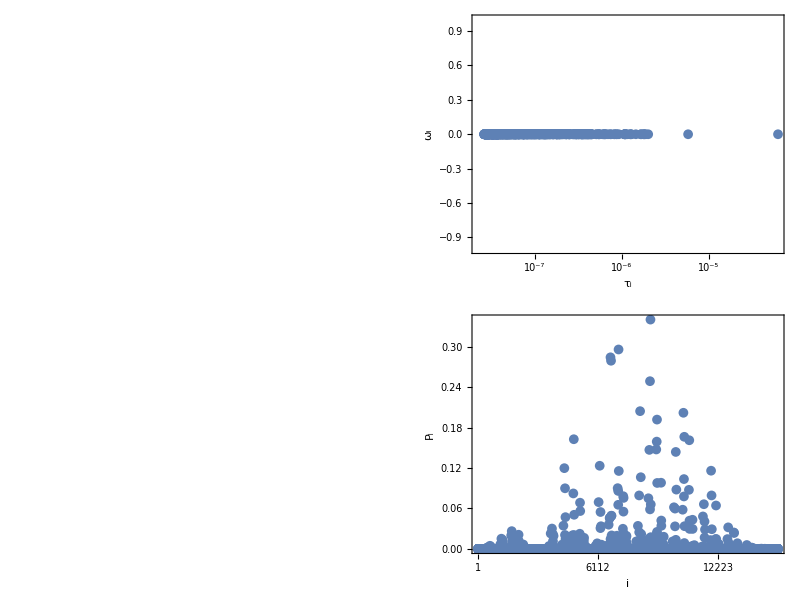

{3 (H_1)+3 (H_2)+O_1+4 (O_1 H_1)+12 (O_1 H_2)+O_2,2 (H_1)+4 (H_2)+2 (O_1)+3 (O_1 H_1)+12 (O_1 H_2)+O_2,2 (H_1)+5 (H_2)+O_1+3 (O_1 H_1)+11 (O_1 H_2)+2 (O_2),2 (H_1)+4 (H_2)+O_1+5 (O_1 H_1)+11 (O_1 H_2)+O_2,3 (H_1)+4 (H_2)+O_1+2 (O_1 H_1)+12 (O_1 H_2)+2 (O_2)}

3259.18

2.8233

-2.6313×10^-8+0. ⅈ

```mathematica
filebase="data/h2o2/9/"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListLogLinearPlot[{-1/Re[#],Im[#]}&/@evals[[1;;-2]],ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Subscript[ω,i]}]],None},{DisplayForm[RowBox[{Subscript[τ,i]}]],Subscript[λ,i]==1/Subscript[τ,i]+I*Subscript[ω,i]}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
Total[spforms*#]&/@multiindices[[Reverse[Ordering[Abs[evecs[[-1]]]]][[1;;5]]]]
Re[Total[temperatures*evecs[[-1]]]/Total[evecs[[-1]]]]
Re[Total[pressures*evecs[[-1]]]/Total[evecs[[-1]]]]
1/evals[[1]]
```

```mathematica
o2dats={};
h2dats={};
h2odats={};
radicaldats={};
temperaturedats={};
pressuredats={};
initials={};
filebase0="data/h2o2/"
ind=1;
AppendTo[initials,multiforms[[ind]]];
α=PseudoInverse[Transpose[evecs]].SparseArray[{ind->1},{dim}];
t0=10^-8;
t1=10^-2;
num=25;
num2=10;
times=Table[t0*(t1/t0)^(i/num),{i,0,num}];
o2norm=DiagonalMatrix[((#[[4]])/Total[#])&/@multiindices];
h2norm=DiagonalMatrix[((#[[1]])/Total[#])&/@multiindices];
h2onorm=DiagonalMatrix[((#[[6]])/Total[#])&/@multiindices];
radicalnorm=DiagonalMatrix[((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices];
temperaturenorm=DiagonalMatrix[temperatures];
pressurenorm=DiagonalMatrix[pressures];
h2=evecs.h2norm;
o2=evecs.o2norm;
h2o=evecs.h2onorm;
rad=evecs.radicalnorm;
temp=evecs.temperaturenorm;
pres=evecs.pressurenorm;

AppendTo[o2dats,Table[{times[[n]],Total[ParallelSum[α[[i]]*Exp[evals[[i]]*times[[n]]]*o2[[i]],{i,First/@Position[evals,u_/;Abs[u]<10^2/times[[n]]]}]]},{n,1,Length[times]}]];
AppendTo[h2dats,Table[{times[[n]],Total[ParallelSum[α[[i]]*Exp[evals[[i]]*times[[n]]]*h2[[i]],{i,First/@Position[evals,u_/;Abs[u]<10^2/times[[n]]]}]]},{n,1,Length[times]}]];
AppendTo[h2odats,Table[{times[[n]],Total[ParallelSum[α[[i]]*Exp[evals[[i]]*times[[n]]]*h2o[[i]],{i,First/@Position[evals,u_/;Abs[u]<10^2/times[[n]]]}]]},{n,1,Length[times]}]];
AppendTo[radicaldats,Table[{times[[n]],Total[ParallelSum[α[[i]]*Exp[evals[[i]]*times[[n]]]*rad[[i]],{i,First/@Position[evals,u_/;Abs[u]<10^2/times[[n]]]}]]},{n,1,Length[times]}]]; 
AppendTo[temperaturedats,Table[{times[[n]],Total[ParallelSum[α[[i]]*Exp[evals[[i]]*times[[n]]]*temp[[i]],{i,First/@Position[evals,u_/;Abs[u]<10^2/times[[n]]]}]]},{n,1,Length[times]}]]; 
AppendTo[pressuredats,Table[{times[[n]],Total[ParallelSum[α[[i]]*Exp[evals[[i]]*times[[n]]]*pres[[i]],{i,First/@Position[evals,u_/;Abs[u]<10^2/times[[n]]]}]]},{n,1,Length[times]}]]; 


p=Legended[Grid[{{ListLogLinearPlot[h2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[o2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[{#[[1]],#[[2]]}&/@#&/@radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[h2odats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[temperaturedats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[pressuredats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]}}],Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]]
```

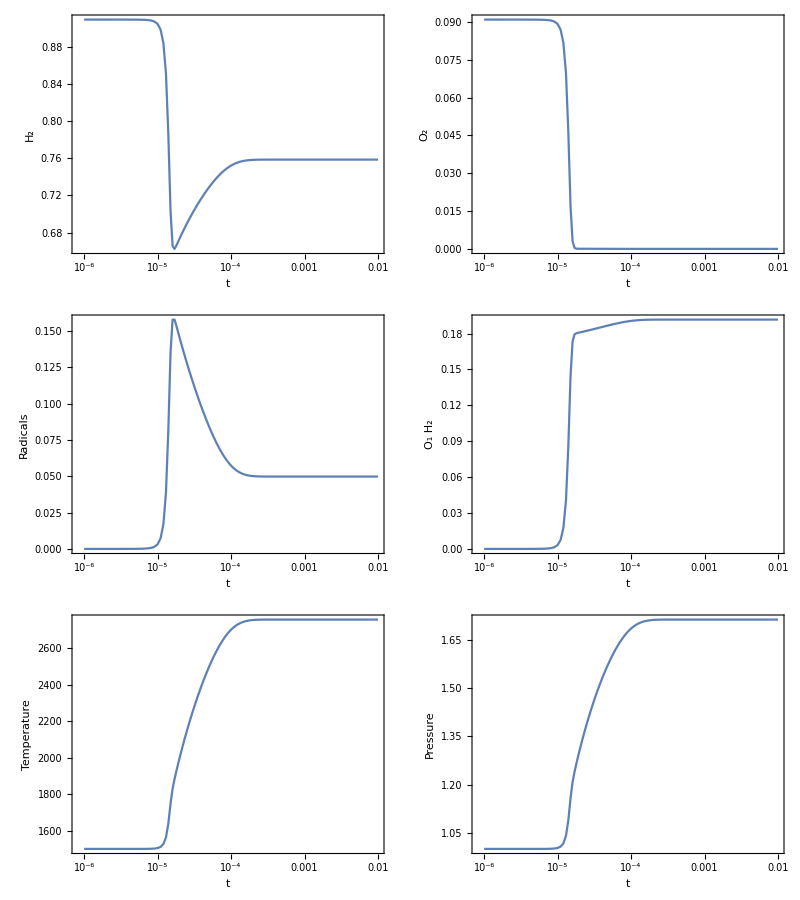

```mathematica
dat=Import["combustion.csv"];
Grid[{{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,4]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,7]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,5]]+dat[[2;;-1,6]]+dat[[2;;-1,8]]+dat[[2;;-1,10]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,9]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,2]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,3]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]}}]
```

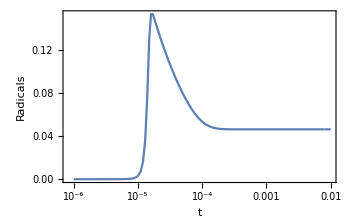

```mathematica
ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,5]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]
```

```mathematica
dat[[1]]
```

{t,T,P,[H2],[H],[O],[O2],[OH],[H2O],[HO2],[H2O2],[AR],'O':2.0->'O2':1.0 Flux,'H':1.0+'O':1.0->'OH':1.0 Flux,'H2':1.0+'O':1.0->'H':1.0+'OH':1.0 Flux,'HO2':1.0+'O':1.0->'O2':1.0+'OH':1.0 Flux,'H2O2':1.0+'O':1.0->'HO2':1.0+'OH':1.0 Flux,'H':1.0+'O2':1.0->'HO2':1.0 Flux,'H':1.0+'O2':2.0->'HO2':1.0+'O2':1.0 Flux,'H':1.0+'H2O':1.0+'O2':1.0->'H2O':1.0+'HO2':1.0 Flux,'AR':1.0+'H':1.0+'O2':1.0->'AR':1.0+'HO2':1.0 Flux,'H':1.0+'O2':1.0->'O':1.0+'OH':1.0 Flux,'H':2.0->'H2':1.0 Flux,'H':2.0+'H2':1.0->'H2':2.0 Flux,'H':2.0+'H2O':1.0->'H2':1.0+'H2O':1.0 Flux,'H':1.0+'OH':1.0->'H2O':1.0 Flux,'H':1.0+'HO2':1.0->'H2O':1.0+'O':1.0 Flux,'H':1.0+'HO2':1.0->'H2':1.0+'O2':1.0 Flux,'H':1.0+'HO2':1.0->'OH':2.0 Flux,'H':1.0+'H2O2':1.0->'H2':1.0+'HO2':1.0 Flux,'H':1.0+'H2O2':1.0->'H2O':1.0+'OH':1.0 Flux,'H2':1.0+'OH':1.0->'H':1.0+'H2O':1.0 Flux,'OH':2.0->'H2O2':1.0 Flux,'OH':2.0->'H2O':1.0+'O':1.0 Flux,'HO2':1.0+'OH':1.0->'H2O':1.0+'O2':1.0 Flux,'H2O2':1.0+'OH':1.0->'H2O':1.0+'HO2':1.0 Flux,'H2O2':1.0+'OH':1.0->'H2O':1.0+'HO2':1.0 Flux,'HO2':2.0->'H2O2':1.0+'O2':1.0 Flux,'HO2':2.0->'H2O2':1.0+'O2':1.0 Flux,'HO2':1.0+'OH':1.0->'H2O':1.0+'O2':1.0 Flux}